## Initialization

```mathematica
$HistoryLength=0;
nbd=NotebookDirectory[];

packageDirectory:="D:\\Mathematica_Packages\\"

Import[packageDirectory<>"QuantileRegression.m"];

<<MaTeX`

SetOptions[
ListPlot,
{Frame->True,FrameStyle->{Black,Bold},TicksStyle->{Black,Bold},LabelStyle->{Black,Bold,fontSize},ImageSize->Large,GridLines->Automatic}
];

SetOptions[
ListLinePlot,
{Frame->True,FrameStyle->{Black,Bold},TicksStyle-> {Black,Bold},LabelStyle->{Black,Bold,fontSize},PlotStyle->Automatic,Filling->None,ImageSize->Large,GridLines->Automatic}
];

SetOptions[
ImageHistogram,
{Frame->True,FrameStyle->{Black,Bold},TicksStyle->{Black,Bold},LabelStyle->{Black,Bold,fontSize},ImageSize->Large,GridLines->Automatic}
];

SetOptions[
Histogram,
{Frame->True,FrameStyle->{Black,Bold},TicksStyle-> {Black,Bold},LabelStyle->{Black,Bold,fontSize},ImageSize->Large,GridLines->Automatic}
];

launchNukes[useKernels_]:=If[
Length@Kernels[]<#,
#-Length@Kernels[]//LaunchKernels,
Nothing
]&@useKernels;


progress[x_,y_]:=TableForm@
{
"Processing...",
ProgressIndicator@Dynamic[x/y//N],
ToString@Round@x<>"/"<>ToString@y,
ToString@PercentForm[x/y//N,DefaultPrintPrecision->1]
}

memoryCheck[]:="Memory in use: "<>ToString[MemoryInUse[]/1024^3//N]<>" Gb"//Print

memoryCleanupStart[]:=Module[{},
"Memory in use: "<>ToString[MemoryInUse[]/1024^3//N]<>" Gb"//Print;
Unprotect@Out;
CloseKernels[];
ClearSystemCache[];
]

memoryCleanupFinalize[]:=Module[{},
Clear@Out;
Protect@Out;
LaunchKernels@useKernels;
"Memory in use after cleanup: "<>ToString[MemoryInUse[]/1024^3//N]<>" Gb"//Print
]


useKernels=2*$ProcessorCount;
launchNukes@useKernels;
SetSharedVariable@monitorCounter;
fontSize=16;
```

Import::nffil: File D:\Mathematica_Packages\QuantileRegression.m not found during Import.

## Functions

```mathematica
getListFromADDstring[dataString_]:="{"<>#<>"}"&@StringReplace[
#,{","->".",WhitespaceCharacter->","}
]&@dataString//StringReplace[
#,{",}"->"}","{,"->"{"}
]&//ToExpression

getCleanImageUDV[image_]:=Colorize[
#,ColorFunction->ColorData[colorFunctionUDV]
]&@ImageReflect@HistogramTransform@image

splitDropAt2D[list_,cuts_]:=Module[
{starts,ends},
starts=Prepend[cuts+1,1];
ends=Append[cuts-1,Length@list];

Pick[
MapThread[
Take[list,{#1,#2},All]&,{starts,ends}
],Thread[starts≤ends]
]
]


getMeanWithDeviation[data_]:=Around@@{Mean@#,StandardDeviation@#}&@data
getMedianWithMedDeviation[data_]:=Around@@{Median@#,MedianDeviation@#}&@data
getHalfQWithQDeviation[data_]:=Around@@{Quantile[#,1/2],QuartileDeviation@#}&@data


getProfilePlot[data_]:=ListLinePlot[
data,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive[Automatic,Opacity@0.25],
PlotRange->profilePlotRange,PlotLegends->SwatchLegend@Automatic
]


getProfileFromStateImage[image_,profileMethod_]:=Module[
{imageFiltered,imageFilteredData},

imageFiltered=TotalVariationFilter[
#,constraintRelaxTV,Method->noiseModelTV
]&@image;

imageFilteredData=ImageData@imageFiltered;
profileMethod/@imageFilteredData
]
```

## >> Data Import <<

```mathematica
dataFolder="E:\\ECHO_METAL_DAY2_MEAS";

SetDirectory@dataFolder;
fileFormat=".ADD";

dataFileID=10;

dataFile=#[[dataFileID]]&@Select[
FileNames["*"<>fileFormat],
Not@StringContainsQ[#,"Stat"]&
]
```

650.ADD

```mathematica
dataUDVraw=Import[dataFolder<>$PathnameSeparator<>dataFile,"Data"];//AbsoluteTiming
dataUDVraw[[1;;8]]//TableForm
```

{0.120471,Null}

ASCUDOPV4.03.4 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Memo_Comments |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Gate Depth [mm] |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
42 | 97	43 | 43	43 | 89	44 | 34	44 | 80	45 | 26	45 | 71	46 | 17	46 | 63	47 | 08	47 | 54	48 | 00	48 | 45	48 | 91	49 | 37	49 | 82	50 | 28	50 | 74	51 | 19	51 | 65	52 | 11	52 | 56	53 | 02	53 | 48	53 | 93	54 | 39 | 
Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	Amp	TBD [ms]	No block	Channel |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
24 | 0	8 | 0	16 | 0	40 | 0	48 | 0	40 | 0	24 | 0	16 | 0	56 | 0	280 | 0	600 | 0	816 | 0	888 | 0	896 | 0	856 | 0	728 | 0	528 | 0	360 | 0	304 | 0	320 | 0	296 | 0	192 | 0	40 | 0	112 | 0	160 | 0	136 | 0	0 | 00	1	4
24 | 0	32 | 0	56 | 0	72 | 0	80 | 0	72 | 0	64 | 0	56 | 0	48 | 0	40 | 0	32 | 0	48 | 0	72 | 0	88 | 0	112 | 0	144 | 0	200 | 0	224 | 0	200 | 0	136 | 0	72 | 0	40 | 0	48 | 0	48 | 0	40 | 0	40 | 0	3 | 20	1	4

```mathematica
getListFromADDstring[dataString_]:="{"<>#<>"}"&@StringReplace[
#,{","->".",WhitespaceCharacter->","}
]&@dataString//StringReplace[
#,{",}"->"}","{,"->"{"}
]&//ToExpression
```

52

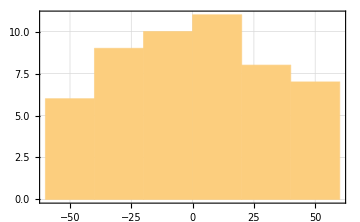

4630

```mathematica
gateDepthMm=First@getListFromADDstring@ToString@dataUDVraw[[5]];
gateDepthMm//Length
Differences@gateDepthMm//Histogram[#,"FreedmanDiaconis",ImageSize->Medium]&
dataUDVraw[[7;;All]]//Length
```

```mathematica
velocityDataGatesMm=First@getListFromADDstring@ToString@#&/@dataUDVraw[[7;;All]]//Parallelize;//AbsoluteTiming
```

{0.394145,Null}

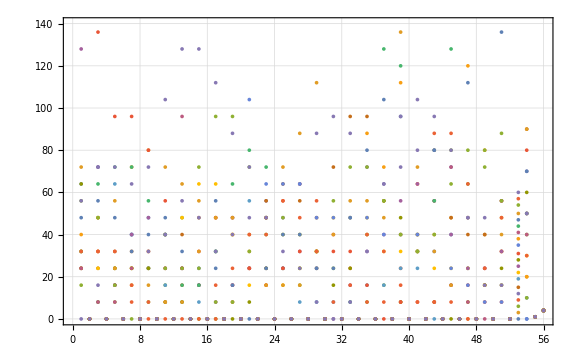

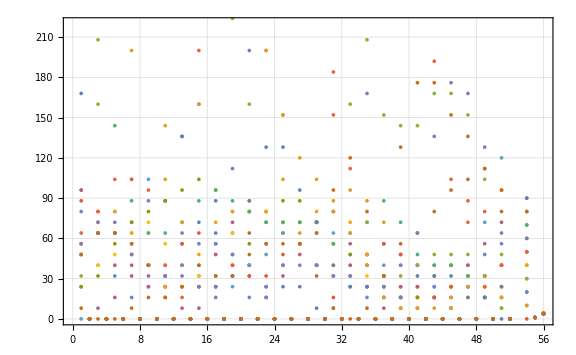

```mathematica
testGateIndex=Min[2000,Length@velocityDataGatesMm];
velocityDataGatesMm[[1;;20]]//ListPlot
velocityDataGatesMm[[testGateIndex-20;;testGateIndex]]//ListPlot
```

## Mixer RPM State Identification

```mathematica
colorFunctionSet={
{"RedBlueTones","Reverse"},
"AvocadoColors",
"SunsetColors",
"BlueGreenYellow"
};

colorFunctionUDV=colorFunctionSet[[1]];
```

{4630,56}

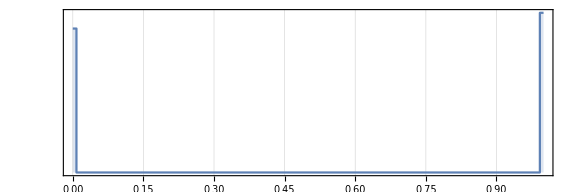

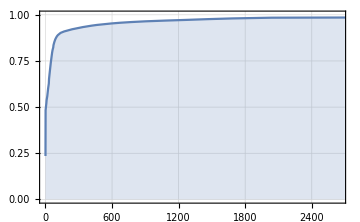

-Graphics-

```mathematica
dataRawImage=Image@Transpose@velocityDataGatesMm;
dataRawImage//ImageDimensions
dataRawImage//ImageHistogram

HistogramTransformInterpolation@dataRawImage//ListLinePlot[
#,Filling->Axis,ImageSize->Medium
]&

getCleanImageUDV@dataRawImage//Image[#,ImageSize->Scaled@2]&
```

Defaults :
   
constraintRelaxTV=0.5;
noiseModelTV=”Laplacian”;

```mathematica
constraintRelaxTV=0.25;
noiseModelTV="Laplacian";
```

```mathematica
dataImageFiltered=TotalVariationFilter[
#,constraintRelaxTV,Method->noiseModelTV
]&@dataRawImage;//AbsoluteTiming

getCleanImageUDV@dataImageFiltered//Image[#,ImageSize->Scaled@2]&
```

{0.138408,Null}

-Graphics-

Defaults :
   
gateCutoff=-5;

```mathematica
gateCutoff=-5;
```

```mathematica
dataFiltered=Transpose@#[[1;;gateCutoff]]&@ImageData@dataImageFiltered;

Manipulate[
ListLinePlot[#,AspectRatio->1/5,PlotRange->{Automatic,{0,0.5}},ImageSize->Scaled@1,Mesh->All,PlotStyle-> PointSize@0.005]&@#[[k]]&@Rescale@dataFiltered,
{k,1,Length@Transpose@ImageData@dataImageFiltered,1}
]
```

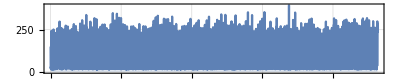

```mathematica
signalRPMraw=Mean/@dataFiltered;
signalRPMraw//ListLinePlot[#,AspectRatio->1/5,ImageSize->Scaled@1,Filling->Axis,PlotRange->All]&
```

Defaults :
   
constraintRelaxSignalLaplacian=10;
constraintRelaxSignalPoisson=0.1;

```mathematica
constraintRelaxSignalLaplacian=10;
constraintRelaxSignalPoisson=0.1;
signalThresholdFactor=0.5;
```

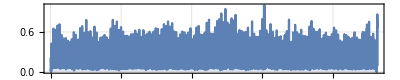

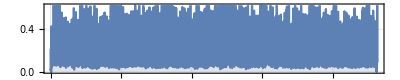

```mathematica
signalRPMfiltered=TotalVariationFilter[
#/TotalVariationFilter[#,constraintRelaxSignalLaplacian,Method->"Laplacian"]&@signalRPMraw,constraintRelaxSignalPoisson,Method->"Poisson"
]//Rescale;

signalRPMfiltered//ListLinePlot[#,AspectRatio->1/5,ImageSize->Scaled@1,Filling->Axis,PlotRange->All]&
signalRPMfiltered//ListLinePlot[#,AspectRatio->1/5,ImageSize->Scaled@1,Filling->Axis]&
```

0.169922

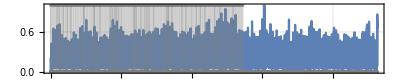

```mathematica
signalRPMthreshold=signalThresholdFactor*FindThreshold[#,Method->"Entropy"]&@ImageAdjust@Image@{signalRPMfiltered}

signalRPMpeakMask=PeakDetect[
signalRPMfiltered,Automatic,Automatic,signalRPMthreshold
];

Show[{
signalRPMfiltered//ListLinePlot[#,AspectRatio->1/5,ImageSize->Scaled@1,Filling->Axis,PlotRange->All]&,
signalRPMpeakMask//ListPlot[#,Filling->Axis,PlotStyle->Directive[Gray,PointSize@0.005]]&
}]
```

timeStepMiliseconds = 12.5;

```mathematica
timeStepMiliseconds=3.2;
```

```mathematica
setPointRPM=ToExpression@StringDelete[#,"RPM"]&@StringDelete[#,fileFormat]&@dataFile

measuredRPM=(Total@signalRPMpeakMask/2)/(timeStepMiliseconds*(Length@signalRPMpeakMask-1)/1000/60)

errorRelativeRPM=Abs[#-setPointRPM]/#&@measuredRPM;
errorRelativeRPM//PercentForm
```

650

453.662

43.28%